```mathematica
PDF[GammaDistribution[A,B],L1]
```

Piecewise[{{(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A], L1>0}, {0, True}}]

```mathematica
Integrate[(ⅇ^-L1 L1^x)/(x!)(ⅇ^-L2 L2^y)/(y!),L1,L2]
```

(Gamma[1+x,L1] Gamma[1+y,L2])/(x! y!)

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!),{L1,0,Infinity},Assumptions->{A>0,B>0,x≥0}]
```

(B^x (1+B)^(-A-x) Gamma[A+x])/(x! Gamma[A])

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!)(ⅇ^-L2 L2^y)/(y!),{L1,0,Infinity},{L2,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0}]
```

((B/(1+B))^(x+y) (1+B)^(-2 A) Gamma[A+x] Gamma[A+y])/(x! y! Gamma[A]^2)

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!)(ⅇ^-L1 L1^y)/(y!),{L1,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0}]
```

(B^-A (B/(1+2 B))^(A+x+y) Gamma[A+x+y])/(x! y! Gamma[A])

```mathematica
BF[A_,B_,x_,y_]:=(B^-A (B/(1+2 B))^(A+x+y) Gamma[A+x+y])/(x! y! Gamma[A])/(((B/(1+B))^(x+y) (1+B)^(-2 A) Gamma[A+x] Gamma[A+y])/(x! y! Gamma[A]^2))
```

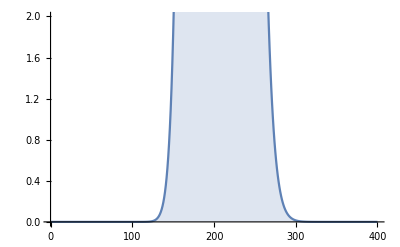

```mathematica
DiscretePlot[BF[1,40,200,n],{n,0,400},PlotRange->{All,{0,2}}]
```

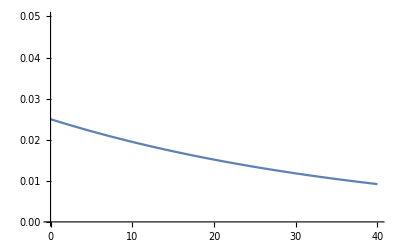

```mathematica
Plot[PDF[GammaDistribution[1,40],x],{x,0,40},PlotRange->{All,{0,0.05}}]
```

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!)(ⅇ^-L2 L2^y)/(y!)(ⅇ^-L1 L1^z)/(z!)(ⅇ^-L2 L2^w)/(w!),{L1,0,Infinity},{L2,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0,z≥0,w≥0}]
```

(B^(-2 A) (B/(1+2 B))^(2 A+w+x+y+z) Gamma[A+w+y] Gamma[A+x+z])/(w! x! y! z! Gamma[A]^2)

```mathematica
Integrate[(B^-A ⅇ^(-L1/B) L1^(-1+A))/Gamma[A](B^-A ⅇ^(-L2/B) L2^(-1+A))/Gamma[A](B^-A ⅇ^(-L3/B) L3^(-1+A))/Gamma[A](B^-A ⅇ^(-L4/B) L4^(-1+A))/Gamma[A](ⅇ^-L1 L1^x)/(x!)(ⅇ^-L2 L2^y)/(y!)(ⅇ^-L3 L3^z)/(z!)(ⅇ^-L4 L4^w)/(w!),{L1,0,Infinity},{L2,0,Infinity},{L3,0,Infinity},{L4,0,Infinity},Assumptions->{A>0,B>0,x≥0,y≥0,z≥0,w≥0}]
```

((B/(1+B))^(w+x+y+z) (1+B)^(-4 A) Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(w! x! y! z! Gamma[A]^4)

```mathematica
BF[A_,B_,{x_,y_},{z_,w_}]:=(B^(-2 A) (B/(1+2 B))^(2 A+w+x+y+z) Gamma[A+w+y] Gamma[A+x+z])/(w! x! y! z! Gamma[A]^2)/(((B/(1+B))^(w+x+y+z) (1+B)^(-4 A) Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(w! x! y! z! Gamma[A]^4))
```

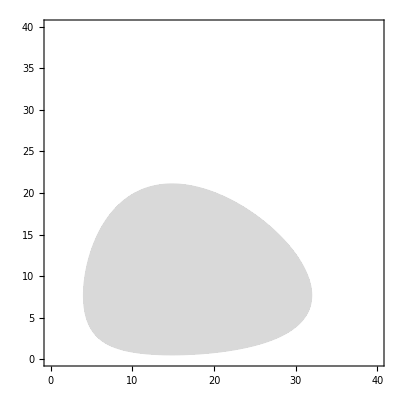

```mathematica
With[{x=15,y=8},DensityPlot[BF[1,40,{x,y},{z,w}],{z,0,40},{w,0,40},ColorFunction->(LightGray&),RegionFunction->Function[{z,w,p},BF[1,40,{x,y},{z,w}]>1],BoundaryStyle->Red]]
```

```mathematica
Exp[Log[B^(-2 A) (B/(1+2 B))^(2 A+w+x+y+z)]+LogGamma[A+w+y]+LogGamma[A+x+z]-LogGamma[w+1]-LogGamma[x+1]-LogGamma[y+1]-LogGamma[z+1]-2LogGamma[A]]
```

```mathematica
BF[A_,B_,{x_,y_},{z_,w_}]:=Exp[-2A Log[B]+(2 A+w+x+y+z)Log[ B/(1+2 B)]+LogGamma[A+w+y]+LogGamma[A+x+z]-LogGamma[w+1]-LogGamma[x+1]-LogGamma[y+1]-LogGamma[z+1]-2LogGamma[A]]/(((B/(1+B))^(w+x+y+z) (1+B)^(-4 A) Gamma[A+w] Gamma[A+x] Gamma[A+y] Gamma[A+z])/(w! x! y! z! Gamma[A]^4))
```

```mathematica
-2A Log[B]+(2 A+w+x+y+z)Log[ B/(1+2 B)]
```

Log[B^(-2 A) (B/(1+2 B))^(2 A+w+x+y+z)]